```mathematica
CalculateMathieuEnergies[n_,k_,q_] :=
	Module[{data},
data=Table[MathieuCharacteristicA[i,j]//N,{i,-1*k,k,2*k/(n-1)},{j,-1*q,q,2*q/(n-1)}];
Export["Mathieu_values.json",data,"ExpressionJSON"];]
```

```mathematica
CalculateMathieuEnergies[500,5,1.0*3.8589003840022436]
```

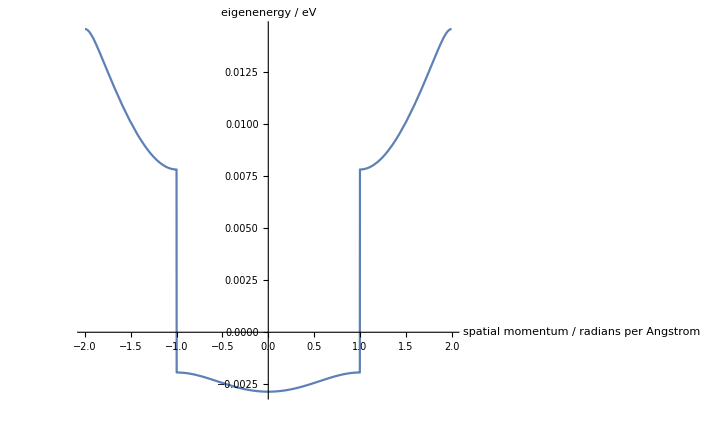

```mathematica
Plot[MathieuCharacteristicA[r,0.01*132.5520520861412]*π^2*(10^10/157.86353)^2*(6.626*10^-34)^2/2/2/π/π/2/(9.11*10^-31)/0.4/(1.60022*10^-19),{r,-2,2}, Axes-> True, AxesLabel->{"spatial momentum / radians per Angstrom","eigenenergy / eV"}]
```

```mathematica
CalculateMathieuFunctions[filename_,nx_,ny_,emin_,emax_,A_,r_,k_] :=
	Module[{data},
data=Table[MathieuC[e,A*k,x*π]//N,{e,emin*k*2,emax*k*2,(emax-emin)*k*2/(ny-1)},{x,-r/2,r/2,r/(nx-1)}];
Export["Mathieu_functions_" <> ToString[filename] <> "_" <> ToString[A] <> "_" <> ToString[nx] <> "x"  <> ToString[ny] <> ".json",data,"ExpressionJSON"];]
```

```mathematica
CalculateMathieuFunctions["long",250,500,-0.05,0.95,0.05,1,132.5520520861412]
```

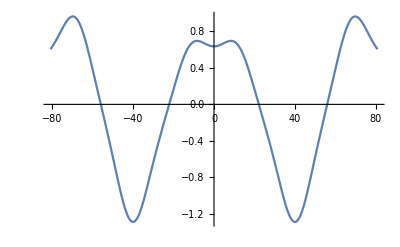

```mathematica
Plot[MathieuC[0.35570564246654207,0.1*3.8589003840022436,z*0.037126125988993584*π],{z,-3/0.037126125988993584,3/0.037126125988993584}]
```

```mathematica
MathieuCharacteristicA[0.7,0.1*3.8589003840022436]
```

0.355706